# How Much Fuel will it Take to Get to Mars with the Delta II Rocket? Adam Eckstein, Gabriel Glen, Nakul RAO

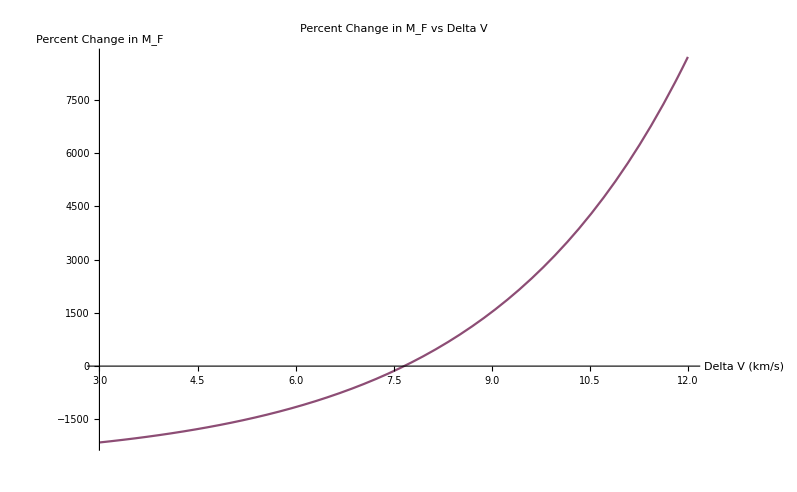

```mathematica
(*Gravitional Constant*)
Subscript[g, 0]=9.80665;

(*Times (s) that each of the Stages run for*)
stage1 = 265;
stage2 = 431;
stage3 =87;

(*Total Burn Time (s)*)
BurnTime = stage1+stage2+stage3;

(*Isp Values at each stage*)
Isp1 = 302;
Isp2 = 319;
Isp3 = 286;

(*Weighted Average (s)*)
WeightedAvg = (stage1/BurnTime) * Isp1 + (stage2/BurnTime)*Isp2 + (stage3/BurnTime)*Isp3;

(*Determine Isp at time(t)*)
Isp := Function[{time, stage1, stage2, stage3},
Which[
time > 0 && time ≤ stage1, 302, 
time > stage1 && time ≤ stage1 + stage2, 319, 
time > stage1 + stage2 && time≤ BurnTime, 286,
time > stage3, 0.00000001
]
];

(*Graph of Isp at a time (t) between 0 and BurnTime*)
ListPlot[Table[Isp[t, stage1, stage2, stage3],{t,0,BurnTime}], AxesLabel->{"Time (s)", "Isp (s)"}, PlotLabel->"Isp of Rocket (s) vs Time (s)", GridLines->{{}, {WeightedAvg}}, GridLinesStyle->Directive[Red, Dashed]];

(*The Inside portion of the DE: Subscript[M, R] * (e^(deltaV/(Isp*Subscript[g, 0])-1)*)
inside = Exp[deltaV(*km/s*)/((WeightedAvg (*s*)* Subscript[g, 0](*m/s^2*)(* m/s / 1000 => km/s*))/1000)]-1(*km/s*);

(*Equation for the Mass of the Fuel*)
massOfFuel = Subscript[M, R]*inside (*kg * Exp[km/s / km/s] = kg*);

(*Plot of the Mass of the Fuel. Varies Subscript[M, R] and deltaV*)
massOfFuelPlot = Plot3D[massOfFuel,{Subscript[M, R],20000(*kg*),30000(*kg*) }, {deltaV, 1, 19},ColorFunction->"Rainbow", AxesLabel->{"Mass of Rocket (kg)", "Delta V (km/s)","Mass of Fuel (kg)"}, PlotLabel->"Mass of Fuel vs Delta V vs Mass of Rocket"];

(*Plot of the Rate of Change of Fuel. Varies Subscript[M, R] and deltaV*)
rateOfChangePlot = Plot3D[inside,{Subscript[M, R],20000,30000},{deltaV, 1, 19}, ColorFunction->"Rainbow", AxesLabel->{"Mass of Rocket (kg)","Delta V (km/s)","Rate of Change of Mass of Fuel"}, PlotLabel->"Rate of Change of Mass of Fuel vs Delta V vs Mass of Rocket"] ;

(*Sensativity Analysis*)
sensativityAnalysis = Plot[((22000(*Chosen Mass of Rocket from Solve Slide*)*inside) - 252279.62 (*Mass of Fuel at chosen deltaV from Solve Slide - 7.66 km/s*))/100, {deltaV, 3, 12},ColorFunction->"Rainbow", AxesLabel->{ "Delta V (km/s)","Percent Change in M_F"}, PlotLabel->"Percent Change in M_F vs Delta V"]

Plot3D[((Subscript[M, R]*inside) - (Subscript[M, R]*Exp[3(* Initial delV value in km/s*)/((WeightedAvg (*s*)* Subscript[g, 0](*m/s^2*)(* m/s / 1000 => km/s*))/1000)]-1(*km/s*)))/100,{Subscript[M, R],20000,30000}, {deltaV, 3, 12},ColorFunction->"Rainbow", AxesLabel->{"Mass of Rocket (kg)", "Delta V (km/s)","Mass of Fuel (kg)"}, PlotLabel->"Mass of Fuel vs Delta V vs Mass of Rocket"];
```